# Лабораторная работа 10. Компьютерные модели аналитической геометрии. Геометрический объект “Точка на плоскости”

Выполнила студентка ММФ БГУ
 1 к, 5 гр. Шклярик В.С.
 10 ноября 2021

### Задание 2.3

```mathematica
ClearAll[kmPoint];
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
```

```mathematica
kmPoint[{1,2}]
```

kmPoint[km,,{1,2}]

### Задание 2.4

```mathematica
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord];
```

```mathematica
kmPoint["A",{1,2}]
```

kmPoint[km,A,{1,2}]

```mathematica
myP=kmPoint["моя Точка",{1,0}]
```

kmPoint[km,моя Точка,{1,0}]

### Задание 2.5

```mathematica
kmPoint[{ϕ_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[ϕ],ρ Sin[ϕ]}];
kmPoint[{π/3,2},"pol"]
```

kmPoint[km,,{1,√3}]

### Задание 2.6

```mathematica
kmPoint[id_String,{ϕ_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[ϕ],ρ Sin[ϕ]}]
```

### Задание 2.7

```mathematica
kmPoint[km,id_String,___]["id"]:=If[id=="","Точка",id];
```

```mathematica
kmPoint["A",{1,2}]["id"]
```

A

```mathematica
myP["id"]
```

моя Точка

```mathematica
kmPoint[{5,2}]["id"]
```

Точка

```mathematica
P1["id"]
```

Точка

```mathematica
kmPoint[{π/3,2},"pol"]["id"]
```

Точка

### Задание 2.8

```mathematica
kmPoint[km,_String,coord_List,___]["coord"]:=coord;
```

```mathematica
kmPoint[{π/3,2},"pol"]["coord"]
```

{1,√3}

```mathematica
myP["coord"]
```

{1,0}

```mathematica
t1=kmPoint["t1",{8,0}]
```

kmPoint[km,t1,{8,0}]

```mathematica
t1["coord"]
```

{8,0}

```mathematica
t1["id"]
```

t1

### Задание 2.9

```mathematica
NamedQ[kmPoint[km,id_String,___]]^:=id≠"";
```

```mathematica
?kmPoint
```

```mathematica
DownValues[kmPoint]
```

{HoldPattern[kmPoint[coord:{_,_}]]:>kmPoint[km,,coord],HoldPattern[kmPoint[id_String,coord:{_,_}]]:>kmPoint[km,id,coord],HoldPattern[kmPoint[{ϕ_,ρ_},pol]]:>kmPoint[km,,{ρ Cos[ϕ],ρ Sin[ϕ]}],HoldPattern[kmPoint[id_String,{ϕ_,ρ_},pol]]:>kmPoint[km,id,{ρ Cos[ϕ],ρ Sin[ϕ]}]}

```mathematica
UpValues[kmPoint]
```

{HoldPattern[NamedQ[kmPoint[km,id_String,___]]]:>id≠}

```mathematica
SubValues[kmPoint]
```

{HoldPattern[kmPoint[km,id_String,___][id]]:>If[id==,Точка,id],HoldPattern[kmPoint[km,_String,coord_List,___][coord]]:>coord}

```mathematica
NamedQ[myP]
```

True

```mathematica
NamedQ[kmPoint[{π/3,2},"pol"]]
```

False

### Задание 2.10

```mathematica
?P1
```

```mathematica
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

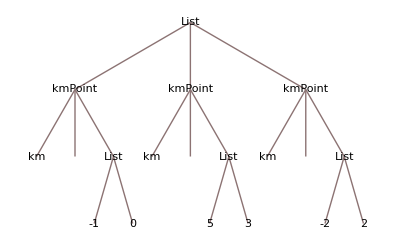

```mathematica
{P1,P2,P3}//TreeForm
```

```mathematica
#["coord"]&/@{P1,P2,P3}
```

{{-1,0},{5,3},{-2,2}}

```mathematica
P1["coord"]
```

{-1,0}

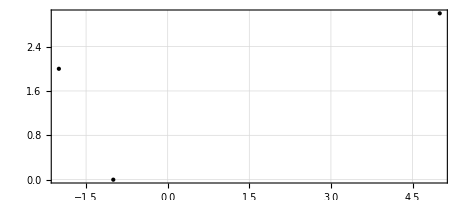

```mathematica
Graphics[Point/@(#["coord"]&/@{P1,P2,P3}),Frame->True,GridLines->Automatic]
```

```mathematica
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts];
```

```mathematica
kmGraphics2D[{P1,P2,P3},Frame->True,GridLines->Automatic]
```

-Graphics-